# Higgs to Zγ via a stop loop (off-shell) - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

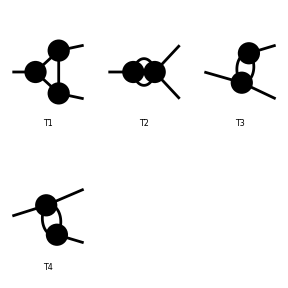

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 31 Classes, and 74 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 74 Particles fields

Restoring 18 field point(s)

in total: 3 Particles insertions

> Top. 1 ad/becf/dedfef.m, 2 diagrams

> Top. 2 ad/bece/dede.m, 1 diagram

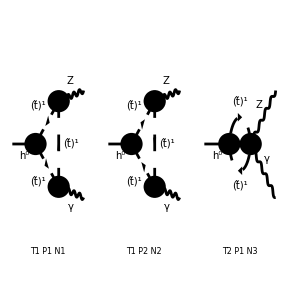

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[2],V[1]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[OffShell[CreateFeynAmp[diag1],2-> mg1,3-> mg2],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp((S(1) | k(1) | Mh0 | {})→(V(2) | k(2) | mg1 | {}
V(1) | k(3) | mg2 | {}))(-1/(π CW2 MW SB SW2)Alfa EL Sub1 Sub6 (Pair1 (1/36 B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))-1/9 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))-1/9 Pair2 Pair3 (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))))

#### Check divergent piece

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp((S(1) | k(1) | Mh0 | {})→(V(2) | k(2) | mg1 | {}
V(1) | k(3) | mg2 | {}))(0)

0

#### Prepare for looptools

Note: polarization sum auto squares the matrix element

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-4.frm

running FORM...

ok

1/(1296 π CW2^2 mg1^2 mg2^2 MW2 SB2 SW2^2)Alfa Alfa2 ((3-4 SW2) USf(1,1,3,3) USfC(1,1,3,3)-4 SW2 USf(1,2,3,3) USfC(1,2,3,3))^2 ((Conjugate[B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))]-4 Conjugate[C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]) ((mg1^4+2 mg1^2 (5 mg2^2-Mh02)+(mg2^2-Mh02)^2) (B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))-4 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))+2 (mg1^6-mg1^4 (mg2^2+3 Mh02)-mg1^2 (mg2^4+2 mg2^2 Mh02-3 Mh02^2)+(mg2^2-Mh02)^3) (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))))+2 (Conjugate[C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]+Conjugate[C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]+Conjugate[C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]) ((mg1^6-mg1^4 (mg2^2+3 Mh02)-mg1^2 (mg2^4+2 mg2^2 Mh02-3 Mh02^2)+(mg2^2-Mh02)^3) (B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))-4 C0i(cc00,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))+2 (mg1^4-2 mg1^2 (mg2^2+Mh02)+(mg2^2-Mh02)^2)^2 (C0i(cc12,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,mg1^2,mg2^2,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))))) (USfC(1,1,3,3) (3 CW MT USf(1,2,3,3) (CA Af(3,3,3)+MUEC SA)+USf(1,1,3,3) (6 CA CW MT2+MW MZ SAB SB (4 SW2-3)))+USfC(1,2,3,3) (3 CW MT USf(1,1,3,3) (CA AfC(3,3,3)+MUE SA)+6 CA CW MT2 USf(1,2,3,3)-4 MW MZ SAB SB SW2 USf(1,2,3,3))) (USf(1,2,3,3) (3 CW MT USfC(1,1,3,3) (CA Af(3,3,3)+MUEC SA)+6 CA CW MT2 USfC(1,2,3,3)-4 MW MZ SAB SB SW2 USfC(1,2,3,3))+USf(1,1,3,3) (3 CW MT USfC(1,2,3,3) (CA AfC(3,3,3)+MUE SA)+USfC(1,1,3,3) (6 CA CW MT2+MW MZ SAB SB (4 SW2-3))))

# Input point

## Inputs

```mathematica
stopM1 = 75;
stopM2 = 10000;
mixT = 0;
muM = 250;
betaA = 1.47; (*tan beta = 10*)
alphaA = betaA - (Pi/2);
offM1 =78;
offM2 = 31;
Clear[matSq,c1,c2,ghSS,h11,h12,h22,z11,z12,z22,m,mh,mZ,mW]
```

# FeynArts Evaluation

## Numerical Evaluation

```mathematica
matPostSub = mat//. mg1 -> offM1//.mg2-> offM2
```

1/(7577354304 π CW2^2 MW2 SB2 SW2^2)Alfa Alfa2 ((3-4 SW2) USf(1,1,3,3) USfC(1,1,3,3)-4 SW2 USf(1,2,3,3) USfC(1,2,3,3))^2 ((Conjugate[B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))]-4 Conjugate[C0i(cc00,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]) (((961-Mh02)^2+12168 (4805-Mh02)+37015056) (B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))-4 C0i(cc00,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))+2 (-6084 (-3 Mh02^2+1922 Mh02+923521)+(961-Mh02)^3-37015056 (3 Mh02+961)+225199600704) (C0i(cc12,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))))+2 (Conjugate[C0i(cc12,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]+Conjugate[C0i(cc2,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]+Conjugate[C0i(cc22,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))]) ((-6084 (-3 Mh02^2+1922 Mh02+923521)+(961-Mh02)^3-37015056 (3 Mh02+961)+225199600704) (B0i(bb0,Mh02,MSf2(1,3,3),MSf2(1,3,3))-4 C0i(cc00,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3)))+2 ((961-Mh02)^2-12168 (Mh02+961)+37015056)^2 (C0i(cc12,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc2,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))+C0i(cc22,6084,961,Mh02,MSf2(1,3,3),MSf2(1,3,3),MSf2(1,3,3))))) (USfC(1,1,3,3) (3 CW MT USf(1,2,3,3) (CA Af(3,3,3)+MUEC SA)+USf(1,1,3,3) (6 CA CW MT2+MW MZ SAB SB (4 SW2-3)))+USfC(1,2,3,3) (3 CW MT USf(1,1,3,3) (CA AfC(3,3,3)+MUE SA)+6 CA CW MT2 USf(1,2,3,3)-4 MW MZ SAB SB SW2 USf(1,2,3,3))) (USf(1,2,3,3) (3 CW MT USfC(1,1,3,3) (CA Af(3,3,3)+MUEC SA)+6 CA CW MT2 USfC(1,2,3,3)-4 MW MZ SAB SB SW2 USfC(1,2,3,3))+USf(1,1,3,3) (3 CW MT USfC(1,2,3,3) (CA AfC(3,3,3)+MUE SA)+USfC(1,1,3,3) (6 CA CW MT2+MW MZ SAB SB (4 SW2-3))))

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=matPostSub//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

```mathematica
feynArtsResult =Chop[MyMatrixElement[stopM1,stopM2,mixT,muM,alphaA,betaA]]
```

0.0294982

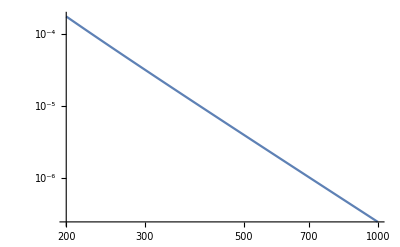

```mathematica
LogLogPlot[{MyMatrixElement[ms,10000,0,250,0,1.47]},{ms,200,1000}]
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (Z or photon)
p2= Momentum of 2nd out-going particle (photon)
mh= Mass of the decaying higgs
m = Mass of the stop
ghss= Higgs-stop coupling
α = Fine structure constant
x and y are Feynman parameters

Additional notation for the Zγ decay:
m1= Mass of the lighter stop mass eignestate
m2= Mass of the heavier stop mass eigenstate
zij= Coupling of the Z boson to stops of mass eigenstates ij = 11, 12, 21, 22
zgij= 4 point coupling of the Z boson and a photon to the stop mass eigenstates
hij= Higgs coupling to stops in their mass eigenstates (note: h11= ghSS)

After introducing all LO and NLO coefficients in this language, I will introduce the explicit dependence of these factors on MSSM parameters. See my summary Latex document for more details.

## Higgs to diphoton (off-shell)

```mathematica
matSq =Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]](*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details*)
```

(9 (8 c1^2 mZ^4+6 c1 c2 mZ^2 (mg1^2+mg2^2-mh^2)+c2^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)))/(2 v^2)

The c1 on-shell term is zero.

```mathematica
c1LOzgInted = 2*((Rational[-1, 6]*e*h11*M2*v*z11*
      (4*mh^2*Sqrt[4*m1^2 - mh^2]*mZ*ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]] + 
       2*Sqrt[4*m1^2 - mh^2]*mZ^3*ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]] + 
       mh^3*(-2*Sqrt[4*m1^2 - mZ^2]*ArcTan[mZ*1/Sqrt[4*m1^2 - mZ^2]] + 
         mZ*(-3 + ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2 - 
           ArcTan[mZ*1/Sqrt[4*m1^2 - mZ^2]]^2)) + 
       mh*mZ*(-4*mZ*Sqrt[4*m1^2 - mZ^2]*ArcTan[mZ*1/Sqrt[4*m1^2 - mZ^2]] + 
         4*m1^2*(ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2 - 
           ArcTan[mZ*1/Sqrt[4*m1^2 - mZ^2]]^2) + 
         mZ^2*(3 + ArcTan[mh*1/Sqrt[4*m1^2 - mh^2]]^2 - 
           ArcTan[mZ*1/Sqrt[4*m1^2 - mZ^2]]^2))))/(mh*mZ*(mh^2 - mZ^2)^3*Pi^2))
```

-1/(3 π^2 mh mZ (mh^2-mZ^2)^3)e h11 M2 v z11 (2 mZ^3 √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh mZ (4 m1^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2)+mZ^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2+3)-4 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2))))+4 mh^2 mZ √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh^3 (mZ ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2-3)-2 √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))))

```mathematica
c2LOzgInted=2*Times[Rational[1,12],e,h11,Power[mh,-1],Power[Plus[Power[mh,2],Times[-1,Power[mZ,2]]],-2],Power[Pi,-2],v,z11,Plus[Power[mh,3],Times[-2,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[1,2]],Power[mZ,2],ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]]],Times[-1,mh,Plus[Power[mZ,2],Times[-2,mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[1,2]],ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]]],Times[2,Power[m1,2],Plus[Times[2,Power[ArcTan[Times[mh,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mh,2]]],Rational[-1,2]]]],2]],Times[-2,Power[ArcTan[Times[mZ,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mZ,2]]],Rational[-1,2]]]],2]]]]]]]]
```

(e h11 v z11 (-mh (2 m1^2 (2 (tan^-1(mh/(√(4 m1^2-mh^2))))^2-2 (tan^-1(mZ/(√(4 m1^2-mZ^2))))^2)-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))+mZ^2)-2 mZ^2 √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh^3))/(6 π^2 mh (mh^2-mZ^2)^2)

```mathematica
c2NLOzgInted=0
```

0

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2+b st^2+2 c ct st

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

a st^2+b ct^2-2 c ct st

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ cot(β)))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
sW->0.4796,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
m1->stopMass1,m2->stopMass2,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

## Plug in values and compare to FeynArts result

```mathematica
c1 = c1LOzgInted//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

1/(6 π^2 cW mh mZ sW (mh^2-mZ^2)^3)e^2 mg2^2 v (ct^2-(4 sW^2)/3) (2 mZ^3 √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh mZ (4 m1^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2)+mZ^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2+3)-4 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2))))+4 mh^2 mZ √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh^3 (mZ ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2-3)-2 √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2))))) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)))

```mathematica
c2 =c2LOzgInted +c2NLOzgInted//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2
```

-1/(12 π^2 cW mh sW (mh^2-mZ^2)^2)e^2 v (ct^2-(4 sW^2)/3) (-mh (2 m1^2 (2 (tan^-1(mh/(√(4 m1^2-mh^2))))^2-2 (tan^-1(mZ/(√(4 m1^2-mZ^2))))^2)-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))+mZ^2)-2 mZ^2 √(4 m1^2-mh^2) tan^-1(mh/(√(4 m1^2-mh^2)))+mh^3) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW)))

```mathematica
matSq
```

1/(2 v^2)9 (1/(144 cW^2 mh^2 (mh^2-mZ^2)^4 π^4 sW^2)(mg1^4+(4 mg2^2-2 mh^2) mg1^2+(mg2^2-mh^2)^2) (ct^2-(4 sW^2)/3)^2 v^2 (mh^3-(2 (2 (tan^-1(mh/(√(4 m1^2-mh^2))))^2-2 (tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2+mZ^2-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh-2 √(4 m1^2-mh^2) mZ^2 tan^-1(mh/(√(4 m1^2-mh^2))))^2 ((-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)) ct^2+(e mt st (At-μ cot(β)) ct)/(mW sW)+st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW)))^2 e^4+1/(9 cW^2 mh^2 (mh^2-mZ^2)^6 π^4 sW^2)2 mg2^4 mZ^2 (ct^2-(4 sW^2)/3)^2 v^2 ((mZ ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2-3)-2 √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh^3+4 √(4 m1^2-mh^2) mZ tan^-1(mh/(√(4 m1^2-mh^2))) mh^2+mZ (4 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2-4 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))+mZ^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2+3)) mh+2 √(4 m1^2-mh^2) mZ^3 tan^-1(mh/(√(4 m1^2-mh^2))))^2 ((-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)) ct^2+(e mt st (At-μ cot(β)) ct)/(mW sW)+st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW)))^2 e^4-1/(12 cW^2 mh^2 (mh^2-mZ^2)^5 π^4 sW^2)mg2^2 (mg1^2+mg2^2-mh^2) mZ (ct^2-(4 sW^2)/3)^2 v^2 (mh^3-(2 (2 (tan^-1(mh/(√(4 m1^2-mh^2))))^2-2 (tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2+mZ^2-2 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh-2 √(4 m1^2-mh^2) mZ^2 tan^-1(mh/(√(4 m1^2-mh^2)))) ((mZ ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2-3)-2 √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))) mh^3+4 √(4 m1^2-mh^2) mZ tan^-1(mh/(√(4 m1^2-mh^2))) mh^2+mZ (4 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2) m1^2-4 mZ √(4 m1^2-mZ^2) tan^-1(mZ/(√(4 m1^2-mZ^2)))+mZ^2 ((tan^-1(mh/(√(4 m1^2-mh^2))))^2-(tan^-1(mZ/(√(4 m1^2-mZ^2))))^2+3)) mh+2 √(4 m1^2-mh^2) mZ^3 tan^-1(mh/(√(4 m1^2-mh^2)))) ((-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)) ct^2+(e mt st (At-μ cot(β)) ct)/(mW sW)+st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW cos(2 β))/(3 cW)))^2 e^4)

```mathematica
myCalcResult = matSq//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

3.58063×10^-10 mg1^4+mg1^2 (1.30969×10^-9 mg2^2-0.0000111895)+2.44821×10^-10 mg2^4-9.27439×10^-6 mg2^2+0.0874176

```mathematica
myCalcResultNum = myCalcResult/. mg1-> offM1 /. mg2->offM2
```

0.0315655

```mathematica
loResult =myCalcResultNum/feynArtsResult
```

1.07008

## Check numerical result of the full expressions for c1 and c2

```mathematica
c1 = 2*((Rational[1, 24]*e*h11*v*(M1*(x - 2*x^2) + M2*(1 - 2*y)*y)*z11)/
     (mZ^2*Pi^2*(m1^2 - M2*y + M2*x*y - mh^2*x*y + M2*y^2 + M1*x*(-1 + x + y))))
```

-(e^2 v (ct^2-(4 sW^2)/3) (M1 (x-2 x^2)+M2 (1-2 y) y) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(24 π^2 cW mZ^2 sW (m1^2+M1 x (x+y-1)+M2 x y+M2 y^2-M2 y-mh^2 x y))

```mathematica
c1 = c1/(e^2 ghSS*v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2 (*Divide these out so we can numerically integrate*)
```

-((ct^2-(4 sW^2)/3) (mg1^2 (x-2 x^2)+mg2^2 (1-2 y) y))/(24 π^2 cW mZ^2 sW (m1^2+mg1^2 x (x+y-1)+mg2^2 x y+mg2^2 y^2-mg2^2 y-mh^2 x y))

```mathematica
c2 =2*Times[Rational[-1,6],e,h11,Power[Pi,-2],v,x,y,Power[Plus[Power[m1,2],Times[-1,M1,x],Times[M1,Power[x,2]],Times[-1,M2,y],Times[-1,Plus[Times[-1,M1],Times[-1,M2],Power[mh,2]],x,y],Times[M2,Power[y,2]]],-1],z11]
```

(e^2 v x y (ct^2-(4 sW^2)/3) ((ct e mt st (At-μ cot(β)))/(mW sW)+ct^2 (-(e mZ (1/2-(2 sW^2)/3) cos(2 β))/(cW sW)-(e mt^2)/(mW sW))+st^2 (-(2 e mZ sW cos(2 β))/(3 cW)-(e mt^2)/(mW sW))))/(6 π^2 cW sW (m1^2-x y (-M1-M2+mh^2)+M1 x^2-M1 x+M2 y^2-M2 y))

```mathematica
c2 =c2/(e^2*ghSS*v)//. ghSS-> h11//.M1->mg1^2//.M2->mg2^2(*Divide these out so we can numerically integrate*)
```

(x y (ct^2-(4 sW^2)/3))/(6 π^2 cW sW (m1^2-x y (-mg1^2-mg2^2+mh^2)+mg1^2 x^2-mg1^2 x+mg2^2 y^2-mg2^2 y))

```mathematica
c1 = c1//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(mg1^2 (1.66463×10^-6 x-8.32315×10^-7) x+mg2^2 (1.66463×10^-6 y-8.32315×10^-7) y)/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+5625.)

```mathematica
c1 = c1 //. mg1-> offM1 //.mg2 -> offM2
```

(6084 (1.66463×10^-6 x-8.32315×10^-7) x+961 (1.66463×10^-6 y-8.32315×10^-7) y)/(-15625. x y+961 y (x+y-1.)+6084 x (x+y-1.)+5625.)

```mathematica
c1 =NIntegrate[c1,{x,0,1},{y,0,(1-x)}]
```

-1.87626×10^-9

```mathematica
c2 = c2//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

(0.0276909 x y)/(mg1^2 x (x+y-1.)+mg2^2 y (x+y-1.)-15625. x y+5625.)

```mathematica
c2 = c2//. mg1-> offM1 //.mg2 -> offM2
```

(0.0276909 x y)/(-15625. x y+961 y (x+y-1.)+6084 x (x+y-1.)+5625.)

```mathematica
c2 =NIntegrate[c2,{x,0,1},{y,0,(1-x)}]
```

4.00651×10^-7

```mathematica
testMatSq = matSq*(e^2*ghSS*v)^2/.ghSS-> h11//.SUBIN[stopM1,stopM2,mixT,muM,betaA]//Simplify
```

3.3771×10^-10 mg1^4+mg1^2 (1.35084×10^-9 mg2^2-0.0000106324)+3.3771×10^-10 mg2^4-0.0000106324 mg2^2+0.0836861

```mathematica
testMatSq = testMatSq/. mg1-> offM1 //.mg2 -> offM2
```

0.0294913

```mathematica
fullResult = testMatSq/feynArtsResult
```

0.999764

# Results

```mathematica
loResult
fullResult
```

1.07008

0.999764